### ‘Seed’ list of colours

```mathematica
initialList={LABColor[0.5187848173343539, 0.6399990176455989, 0.67],LABColor[0.8300000000000001, 0.04, 0.8],LABColor[0.7034977311779242, -0.6348740400535063, 0.62490305423001],LABColor[0.794283848056134, -0.3547323340157605, -0.31862459565533907],LABColor[0.4417864340686453, 0.40076871833601263, -0.8768750645112572],LABColor[0.6263977928344144, 0.8658104149752872, -0.565775642691356]};
```

### The generated path in CIE LAB color space

```mathematica
AbsoluteTiming[
backgroundContours=Table[
ContourPlot3D[
Quiet[
ColorConvert[LABColor[L,a,b],"RGB"]⟦j⟧
]==v
,{L,0,1},{a,-2,2},{b,-2,2}
,ContourStyle->Opacity[0.6]
,Mesh->None
]
,{j,1,3},{v,{0.001,0.999}}];
]
```

{42.261,Null}

```mathematica
Block[{colorList},
colorList=Table[
Blend[{
Range[0,1,1/6],ColorConvert[Join[#,{#⟦1⟧}]&@
initialList
,"LAB"]
}ᵀ,x]
,{x,0,1,0.02}];
Show[
Flatten[{
Graphics3D[{
Line[List@@@colorList],
PointSize[0.03],
{#,Point[List@@#]}&/@colorList
}
,Axes->True
,AxesLabel->{"L","a","b"}
],
backgroundContours
}]
,PlotRange->{{0.3,0.9},{-0.75,1},{-1.2,1.05}}
,ImageSize->650
,BoxRatios->Automatic
]
]
```

-Graphics3D-

### Preliminary calculations

```mathematica
periodicList=Join[initialList,{initialList⟦1⟧}];
```

```mathematica
interpolationPoints=100;
```

```mathematica
colorDifference[{L1_,a1_,b1_},{L2_,a2_,b2_}]:=ColorDistance[LABColor[L1,a1,b1],LABColor[L2,a2,b2],DistanceFunction->"CIE2000"];
```

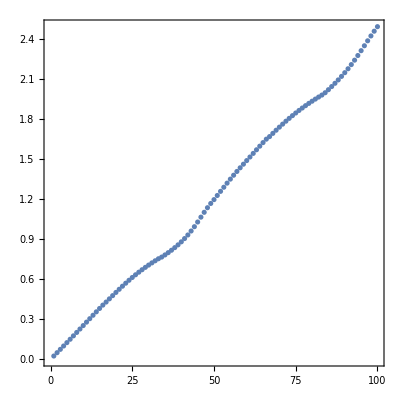

```mathematica
ListPlot[
accumulatedDifferences=Accumulate[
Map[
Apply[colorDifference[#1,#2]&],
Partition[
Table[
Interpolation[
Transpose[{
Range[0,1,1/(Length[periodicList]-1)],
List@@@(ColorConvert[#,"LAB"]&/@periodicList)
}]
,InterpolationOrder->1
][x]
,{x,0,1,1/interpolationPoints}]
,2,1]
]
]
,Frame->True
,AspectRatio->1
]
```

```mathematica
colorList=Table[
{y,
Interpolation[
Transpose[{
Range[0,1,1/(Length[periodicList]-1)],
List@@@(ColorConvert[#,"LAB"]&/@periodicList)
}]
,InterpolationOrder->1
][
Interpolation[
Reverse/@Transpose[{
Range[0,1,1/interpolationPoints],
Join[{0},accumulatedDifferences]/Last[accumulatedDifferences]
}]
][y]
]
}
,{y,0,1,1/interpolationPoints}];
```

### Exporting data

```mathematica
FileSize[
Export[
FileNameJoin[{NotebookDirectory[],"Data.csv"}],
Join[
{{"x","L","a","b","R","G","B"}},
Join[{N[#⟦1⟧]},#⟦2⟧,List@@ColorConvert[LABColor[#⟦2⟧],"RGB"]]&/@colorList
]
,"CSV"
]
]
```

11.559 kB

### Function Definition

```mathematica
PUCCS[x_]=Blend[
Table[
{x,
ColorConvert[
LABColor@@Interpolation[
colorList
,InterpolationOrder->1
][x]
,"RGB"]
}
,{x,0,1,0.01}]
,x]
```

Blend[{{0.,RGBColor[0.8889427469969852, 0.22673227640012172, 0.]},{0.01,RGBColor[0.8956274406155226, 0.27553288030331824, 0.]},{0.02,RGBColor[0.9019507507843885, 0.318608215541461, 0.]},{0.03,RGBColor[0.907905487190649, 0.3580633000693721, 0.]},{0.04,RGBColor[0.9134808162089558, 0.3949845524063657, 0.]},{0.05,RGBColor[0.918668356138916, 0.43002019316005363, 0.]},{0.06,RGBColor[0.923462736751354, 0.4635961938811463, 0.]},{0.07,RGBColor[0.9278609626724071, 0.49601354353255284, 0.]},{0.08,RGBColor[0.9318616057744784, 0.5274983630587982, 0.]},{0.09,RGBColor[0.9354640163365924, 0.5582303922647159, 0.]},{0.1,RGBColor[0.9386675557407496, 0.5883604892249517, 0.004034952213848706]},{0.11,RGBColor[0.9414708123927996, 0.6180221032545026, 0.016031521294251994]},{0.12,RGBColor[0.943870754968487, 0.6473392272576862, 0.029857267582036696]},{0.13,RGBColor[0.9458617774020323, 0.676432172396153, 0.045365670193636125]},{0.14,RGBColor[0.9474345911958609, 0.7054219201084561, 0.06017985923530026]},{0.15,RGBColor[0.9485749196617762, 0.7344334940032564, 0.07418869502646075]},{0.16,RGBColor[0.9492596163836376, 0.7634480277996188, 0.08767517868137237]},{0.17,RGBColor[0.9462308253550155, 0.7922009241807345, 0.10066327128139077]},{0.18,RGBColor[0.9088702681901394, 0.7940579017644396, 0.10139639009534024]},{0.19,RGBColor[0.8716809050191757, 0.7954897210083888, 0.10232311621802098]},{0.2,RGBColor[0.8337524177888596, 0.7965471523787845, 0.10344968926026826]},{0.21,RGBColor[0.7947193410849823, 0.7972381033243311, 0.10477682283894393]},{0.22,RGBColor[0.7540941866826836, 0.7975605026647324, 0.10631182441371936]},{0.23,RGBColor[0.7112894518675287, 0.7974995317311054, 0.1080672415170634]},{0.24,RGBColor[0.6655745739336695, 0.7970267795229349, 0.11006041388465265]},{0.25,RGBColor[0.6160047476007512, 0.7960993904970947, 0.11231257117602686]},{0.26,RGBColor[0.5612859274945571, 0.794659599537827, 0.11484733363789801]},{0.27,RGBColor[0.4994862901720824, 0.7926351396848288, 0.11768844813479104]},{0.28,RGBColor[0.42731393423789277, 0.7899410218414098, 0.12085678487511567]},{0.29,RGBColor[0.3378265607222193, 0.786483110019224, 0.124366774034814]},{0.3,RGBColor[0.2098475715121697, 0.7821998608677176, 0.12819222127525928]},{0.31,RGBColor[0.15061488620640032, 0.7845112116922692, 0.21943537230975235]},{0.32,RGBColor[0.18766933782916642, 0.7905828987725732, 0.31091344246312086]},{0.33,RGBColor[0.21160609617940718, 0.7962175427587832, 0.38519766326885596]},{0.34,RGBColor[0.22717569971119178, 0.8013847719431052, 0.4490960048955565]},{0.35,RGBColor[0.23690087622812944, 0.8061220291668977, 0.5056371468159846]},{0.36,RGBColor[0.24226377668817778, 0.8104638164122776, 0.5563570758573497]},{0.37,RGBColor[0.24424372086048424, 0.8144455902164638, 0.6022301663745243]},{0.38,RGBColor[0.24352232677523483, 0.818107753931944, 0.6440238320299774]},{0.39,RGBColor[0.240562414747303, 0.8214980148949816, 0.6824536572462205]},{0.4,RGBColor[0.2356325204239052, 0.8246710357361025, 0.7182393675419642]},{0.41,RGBColor[0.22880568593963513, 0.8276865975886148, 0.7521146815529203]},{0.42,RGBColor[0.21993360985514526, 0.8306086550266585, 0.7848331944479765]},{0.43,RGBColor[0.20858849290850018, 0.833503273690861, 0.8171544357676854]},{0.44,RGBColor[0.1939295692427068, 0.8364382500400466, 0.8498448067259188]},{0.45,RGBColor[0.17438366103820427, 0.839483669055626, 0.8836865023336339]},{0.46,RGBColor[0.14679145002531463, 0.8427091517444469, 0.9194481212717681]},{0.47,RGBColor[0.10278921007810729, 0.8461971304126238, 0.9580316568065935]},{0.48,RGBColor[0.0013920913109500188, 0.8499626968466341, 0.9995866371771526]},{0.49,RGBColor[0.10740420703601522, 0.8254781216972907, 1.]},{0.5,RGBColor[0.1581725581872408, 0.8008522647497104, 1.]},{0.51,RGBColor[0.19300141807932156, 0.7761561224913385, 1.]},{0.52,RGBColor[0.2194621842292243, 0.751443124097109, 1.]},{0.53,RGBColor[0.2405673704012788, 0.7265803324554873, 1.]},{0.54,RGBColor[0.25788347992973676, 0.701321051230534, 1.]},{0.55,RGBColor[0.2722888922216317, 0.6753950894563805, 1.]},{0.56,RGBColor[0.28422807900785235, 0.6486730893521468, 1.]},{0.57,RGBColor[0.2939073740750084, 0.6212117649042728, 1.]},{0.58,RGBColor[0.301442767979156, 0.5931976878638505, 1.]},{0.59,RGBColor[0.30694603901024253, 0.5648312189065924, 1.]},{0.6,RGBColor[0.3105418468883679, 0.5362525958007331, 1.]},{0.61,RGBColor[0.3123531986526998, 0.5075386530652202, 1.]},{0.62,RGBColor[0.31248922600720636, 0.4787151440558522, 1.]},{0.63,RGBColor[0.31103663081260624, 0.44973844514160927, 1.]},{0.64,RGBColor[0.30803814950244496, 0.4204116611935119, 1.]},{0.65,RGBColor[0.30343473603466015, 0.390226489453496, 1.]},{0.66,RGBColor[0.29717122075330515, 0.3591178757512998, 1.]},{0.67,RGBColor[0.3178994129506999, 0.3295740682997879, 1.]},{0.68,RGBColor[0.3842479358768364, 0.3280946443367561, 1.]},{0.69,RGBColor[0.44293649140770536, 0.3260767554252524, 1.]},{0.7,RGBColor[0.4970845087445758, 0.3234487047238235, 1.]},{0.71,RGBColor[0.5485591109413528, 0.3201099534066949, 1.]},{0.72,RGBColor[0.5985798481027601, 0.3159263917472715, 1.]},{0.73,RGBColor[0.6480500606439057, 0.31071717884730565, 1.]},{0.74,RGBColor[0.6976685401842261, 0.3042411890803418, 1.]},{0.75,RGBColor[0.7479712773579563, 0.29618040787504757, 1.]},{0.76,RGBColor[0.7993701361353484, 0.28611136999256687, 1.]},{0.77,RGBColor[0.8521918014427678, 0.2734527325942473, 1.]},{0.78,RGBColor[0.9067003897516911, 0.2573693489198746, 1.]},{0.79,RGBColor[0.963334644317004, 0.23648492980159264, 1.]},{0.8,RGBColor[1., 0.21867949406239662, 0.9712088595948508]},{0.81,RGBColor[1., 0.21606849746358275, 0.9041480210597966]},{0.82,RGBColor[1., 0.2142183009650403, 0.8419706002336457]},{0.83,RGBColor[1., 0.21295365915197945, 0.7823908751330633]},{0.84,RGBColor[0.9971140114799418, 0.21220068235083267, 0.7256713129328118]},{0.85,RGBColor[0.993273906363258, 0.2118788857127918, 0.671860243327784]},{0.86,RGBColor[0.9887084084529413, 0.21191070453347688, 0.6209624706933893]},{0.87,RGBColor[0.9835846378805114, 0.2122246941077346, 0.5728987835613306]},{0.88,RGBColor[0.9780378159372328, 0.21275878699579343, 0.5274829957183049]},{0.89,RGBColor[0.9721670725313721, 0.21346242315895625, 0.4844270603851604]},{0.9,RGBColor[0.9660363209686843, 0.21429691147008262, 0.4433660148378527]},{0.91,RGBColor[0.9596781387247791, 0.2152344151262528, 0.4038812338146013]},{0.92,RGBColor[0.9530986696850675, 0.21625626438013962, 0.3655130449917989]},{0.93,RGBColor[0.9462863346513658, 0.21735046958786286, 0.327780364198278]},{0.94,RGBColor[0.93921469089265, 0.2185101447033258, 0.2901491717537278]},{0.95,RGBColor[0.9318478255642132, 0.21973168075163751, 0.25198973718066836]},{0.96,RGBColor[0.9241434776436454, 0.22101341980094052, 0.2124579038400577]},{0.97,RGBColor[0.9160532016485884, 0.22235495330179011, 0.17018252385769012]},{0.98,RGBColor[0.90752576202319, 0.22375597459867458, 0.1223073280126531]},{0.99,RGBColor[0.8985077346125597, 0.22521565729028564, 0.05933950582860665]},{1.,RGBColor[0.8889427469969852, 0.22673227640012172, 0.]}},x]

### Benchmarking

#### Strip

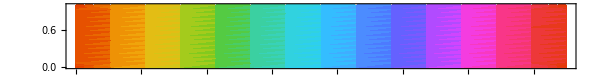

```mathematica
strip=DensityPlot[
x,{x,0,6},{y,0,1}
,ColorFunction->PUCCS
,PlotRangePadding->None
,AspectRatio->1/8
,ImageSize->600
]
```

```mathematica
FileSize[
Export[FileNameJoin[{NotebookDirectory[],"Benchmarks/strip.png"}],strip]
]
```

2.857 kB

#### Kovesi washboard

```mathematica
KovesiWashboardF[x_,y_,f_:50.5,a_:0.05]:=x-a y^2(2x-2 0.5)-y^2 a Cos[f 2π x]
```

```mathematica
washboard=DensityPlot[
KovesiWashboardF[x/6,y,80.5,0.05]
,{x,0,6},{y,0,1}
,AspectRatio->1/2.5
,PlotRangePadding->None
,ImageSize->700
,PlotPoints->200
,ColorFunction->PUCCS
]
```

-Graphics-

```mathematica
FileSize[
Export[FileNameJoin[{NotebookDirectory[],"Benchmarks/washboard.png"}],washboard]
]
```

100.898 kB

#### Circle color scale

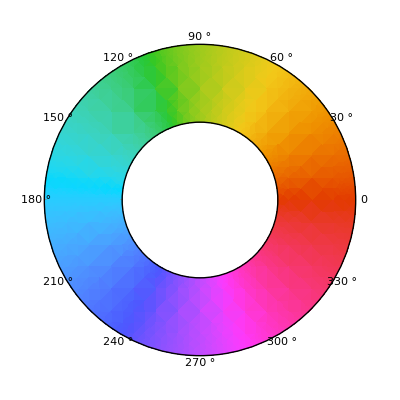

```mathematica
circle=Show[{
DensityPlot[
Arg[(x+ⅈ y)]
,{x,-1,1},{y,-1,1}
,ColorFunction->Function[PUCCS[1/(2π)Mod[#,2π]]]
,ColorFunctionScaling->False
,ExclusionsStyle->PUCCS[0.5]
,RegionFunction->Function[{x,y,f},0.5^2≤x^2+y^2≤1]
,Frame->False
],
Graphics[{
Circle[{0,0},1],
Circle[{0,0},0.5]
}],
Graphics[{
Table[
Text[θ,1.05{Cos[θ],Sin[θ]}]
,{θ,0,359°,30°}]
}],
Graphics[{}]
}
,ImageSize->400
,PlotRange->All
]
```

```mathematica
FileSize[
Export[FileNameJoin[{NotebookDirectory[],"Benchmarks/circle.png"}],circle]
]
```

39.319 kB

#### Donut plot

```mathematica
LGdonut=RegionPlot[
True
,{x,-3,3},{y,-3,3}
,ColorFunction->Function[{x,y},Directive[
Blend[{White,PUCCS[1/2+1/(2π)Arg[(x+ⅈ y)^2]]},Abs[1/ⅇ^-1(x+ⅈ y)^2 Exp[-(x^2+y^2)]]]
]]
,ColorFunctionScaling->False
,PlotRangePadding->None
,PlotPoints->150
,ImageSize->450
]
```

-Graphics-

```mathematica
FileSize[
Export[FileNameJoin[{NotebookDirectory[],"Benchmarks/LGdonut.png"}],LGdonut]
]
```

69.182 kB